# TaX1k 1a

```mathematica
system={X1'[t]==b*(X2[t]+X1[t])-c*X1[t]-X1[t]*(X2[t]+X1[t])/K-a*X1[t]*X2[t],
	X2'[t]== -c*X2[t]-X2[t]*(X2[t]+X1[t])/K+a*X1[t]*X2[t]};

newSystem=system/.{X1'[t]-> 0,X2'[t]-> 0};
sol=Solve[newSystem,{X1[t],X2[t]}];
Print[sol]
```

{{X1[t]→0,X2[t]→0},{X1[t]→b/a,X2[t]→(-b+a b K-a c K)/a},{X1[t]→c/a,X2[t]→-c/a},{X1[t]→(b-c) K,X2[t]→0}}

Here X1 is the number of susceptible and X2 are the number of infected. The first and last fixed points have X2=0, which is the same as not having any infected individuals. These two solutions are therefore not relevant. In the third fixed point, where X1=c/a and X2=-c/a, is also not biologically possible, since we either have negative number of susceptible or infected. Therefore we have only one fixed point that is relevant for this solution, which is

```mathematica
sol[[2]]
```

{X1[t]→b/a,X2[t]→(-b+a b K-a c K)/a}

Now calculate the eigenvalues for the system at the fixed point above and from them calculate K_C.

```mathematica
rhsSystem={system[[1]][[2]],system[[2]][[2]]};
j={{D[system[[1]][[2]], X1[t]],D[system[[2]][[2]], X1[t]]},{D[system[[1]][[2]], X2[t]],D[system[[2]][[2]], X2[t]]}};
eigenValues=Simplify[Eigenvalues[j]/.sol[[2]]]
Reduce[eigenValues[[2]]<0&&eigenValues[[1]]<0&&a>0&&b>0,{a,b,c ,K}]
```

{-b+c,b-a b K+a c K}

a>0&&b>0&&c<b&&K>b/(a b-a c)

a>0\land b>0\land c<b\land K>\frac{b}{a b-a c}

```mathematica
(*Nsystem=rhsSystem[[1]]+rhsSystem[[2]]
Simplify[Nsystem/.{X1[t]+X2[t]-> N}]*)
(*D[N[x,t],t]==N[x,t](b-c-N[x,t]/K)+d*D[N[x,t],x,x]*)
(*From lecture 6 you get the dimensionless variables to r=(b-c)=[t]^-1*)
J={{0,1},{2u-mu,-gamma}}
Eigenvalues[J]
uSystem={U'[t]== V[t],
		V'[t]== -c*V[t]-U[t](mu-U[t])};
```

{{0,1},{-mu+2 u,-gamma}}

{1/2 (-gamma-√(gamma^2-4 mu+8 u)),1/2 (-gamma+√(gamma^2-4 mu+8 u))}

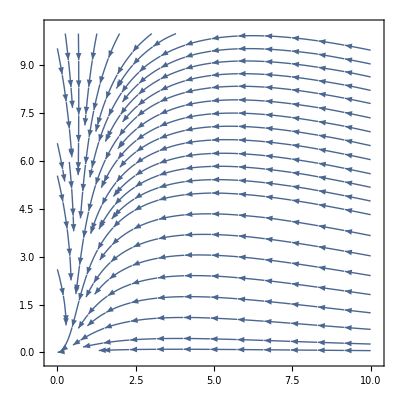

```mathematica
variables={a-> 1,b-> 3,c-> 1,K-> 5};
tmp=rhsSystem/.variables;
StreamPlot[tmp,{X1[t],0,10},{X2[t],0,10}]
```

These solution

```mathematica
fixedPoint=sol[[2]]/.Rule-> Equal;

Reduce[sol[[2]][[2]][[2]]>0&&sol[[2]][[1]][[2]]>0,{a,b,c,K}]
```

(a<0&&b<0&&((c<b&&K>b/(a b-a c))||(c>b&&K<b/(a b-a c))))||(a>0&&b>0&&((c<b&&K>b/(a b-a c))||(c>b&&K<b/(a b-a c))))

```mathematica
(*DEigenvalues[system]*)
(*sol=NDSolve[{system,X1[0]==X2[0]==100},{X1,X2},{t,1000}]*)
```